```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/Andes2/LogProcessing/moment-of-learning

### BKT model recursion

Values from Table 1, "Guess model" of Beck and Chang paper.

```mathematica
vals={ps->0.05, pg->0.3, pt->0.1, p0->0.36};
```

```mathematica
recursion["correct",plast_]:=1-(1-pt)(1-plast) pg/(pg+(1-ps-pg) plast);
recursion["incorrect",plast_]:=1-(1-pt)(1-plast)(1-pg)/(1-pg-(1-ps-pg) plast);
```

Find fixed points of the recursion

```mathematica
fcorrect=Solve[recursion["correct",plast]==plast,plast]
```

{{plast→1},{plast→(pg pt)/(-1+pg+ps)}}

```mathematica
fcorrect/.vals
```

{{plast→1},{plast→-0.0461538}}

```mathematica
fincorrect=Solve[recursion["incorrect",plast]==plast,plast]
```

{{plast→1},{plast→((-1+pg) pt)/(-1+pg+ps)}}

Expansion about fixed points

```mathematica
Simplify[Series[recursion["correct",plast],{plast,1,1}]]
```

1+(pg (-1+pt) (plast-1))/(-1+ps)+O[plast-1]^2

```mathematica
Simplify[Series[recursion["incorrect",plast],{plast,(1-pg) pt/(1-pg-ps),1}]]
```

((-1+pg) pt)/(-1+pg+ps)+(ps (plast-((-1+pg) pt)/(-1+pg+ps)))/((-1+pg) (-1+pt))+O[plast-((-1+pg) pt)/(-1+pg+ps)]^2

If we confine our attention to the region 0<P_j<1, the “j correct” recursion relation has a stable fixed point at 1.  Near that point, convergence is exponentially fast.  Similarly, the “j incorrect” recursion relation has a stable fixed point at (1-P(G)) P(T)/(1-P(G)-P(S)).  Near that point, convergence is also exponentially fast.

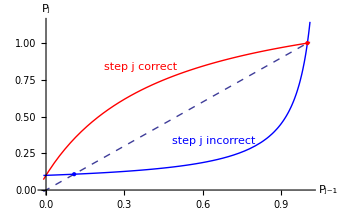

```mathematica
pRecursion=Plot[{plast,recursion["correct",plast]/.vals,recursion["incorrect",plast]/.vals},{plast,-0.01,1.01},Epilog->{PointSize[Large],{Red,Point[{1,1}],Text["step j correct",{0.5,.8},{1,-1}]},{Blue,Point[{1,1} plast/.fincorrect[[2]]/.vals],Text["step j incorrect",{0.8,.3},{1,-1}]}},PlotStyle->{Dashed,Red,Blue},AxesLabel->{Subscript["P","j-1"],Subscript["P","j"]},BaseStyle->{FontSize->12}]
```

```mathematica
Export["p-recursion.eps",pRecursion]
```

p-recursion.eps